# Coarse-graining, Long-range Forecasting, Information Theory and Model Error

## Prof Chen Tianyu Zhu Enze Wang https://github.com/moslandwez March 12

## Reference

Information theory, model error, and predictive skill of stochastic models for complex nonlinear systems (Dimitrios  Giannakis, Andrew J. Majda, Illia Horenko)
-Graphics-

## Content

1.  Information theory, predictability, and model error

   2.  Long-range, coarse-grained forecasts

   3.  An interesting example

   4.  Short- and medium-range forecasts in a nonstationary autoregressive model

## Information theory, predictability, and model error

### Predictability in a perfect-model environment

#### Our Problems

We have a stochastic dynamical system:

 	d z⃗==F(z⃗,t)dt+G(z⃗,t)dW   with z⃗∈R^N

 	which is observed through measurements:

	 x(t)==H(z⃗(t)),  x(t)∈R^n,n≤N

 	where H will be a projection operator to a single mode of this models (especially the dimension of z⃗(t) N is large)

In our following example: z⃗(t) can be something from 3-mode dyad model:

 	dx==(Ix y_1+L_1 y_1+L_2 y_2+F+Dx)dt

 	d y_1==(-I x^2-L_1 x-γ_1 ϵ^-1 y_1)dt+σ_1 ϵ^(-1/2)d W_1

 	d y_2==(-L_2x-γ_2 ϵ^-1 y_2)dt+σ_2 ϵ^(-1/2)d W_2

A_t==A(z⃗(t)) is a target variable for prediction

	X_t=={x(t_i):t_i∈[t-Δτ,t]} (x(t_i) from x(t)==H(z⃗(t))) is history of observation

#### Our Problem

How much information can we get about A_t in the future with uncertainty in A_t both from 



         1. Incomplete measure of

 
     x(t)==H(z⃗(t)),  x(t)∈R^n,n≤N


     2. Stochastic component of 


      d z⃗==F(z⃗,t)dt+G(z⃗,t)dW

#### Important definition 1

1. Predictability is additional information contained in time-dependent probability distribution p(A_t|X_0)


      p(A_t)==∫d X_0 p(A_t|X_0)p(X_0)==∫d X_0 p(A_t,X_0)


      2. Statistical equilibrium state p_eq(z(t)) which is either time-independent or time-periodic


          p_eg(z⃗(t+T))==p_eq(z⃗(t))


       3. z⃗(t) is ergotic


       1/s∑_(i=0)^(s-1) A(z⃗(t-iδt))≈∫d z⃗ p_eq(z⃗)A(z⃗) for large sample s.


        4. X_t,A_t will be the equilibrium distributions induced by p_eq(z⃗(t)):


            p(A_t)==p_eq(A_t),  p(X_t)==p_eq(X_t)

#### Important definition 2

1. Relative entropy:


         P(p'(A_t),p(A_t))==∫d A_t p'(A_t)log(p'(A_t))/(p(A_t))


      2. Bayesian-update interpretation of relative entropy


      P(p(A|X_0),p(A_t))==∫d A_t p(A_t|X_0)logp(A|X_0)-∫d A_t p(A_t|X_0)logp(A_t)

      which means if p'(A_t)==p(A_t|X_0) is the posterior distribution of A_t conditioned on some variable X_0and  then P(p(A|X_0),p(A_t)) measures the additional information beyond p(A_t)about A_t gained by having observed X_0.

#### Important definition 3

1. The natural information-theoretic measure of predictability compatible with the prior distribution p(A_t) 


      D_t^X_0==P(p(A_t|X_0),p_eq(A_t))
 
 
         D_t==∫d X_0 p(X_0)D_t^x_0==∫d X_0∫d A_t p(A_t,X_0)log(p(A_t|X_0))/(p(A_t))
        ==P(p(A_t,X_0),p(A_t)p(X_0))==I(A_t;X_0)
 
 
       the expected predictability of the target variable over initial data.

 
       The mutual information between the source and output  measure the rate of information flow across the channel.

### Quantity error in imperfect models

Distributions p^M(A_t|X_0) from imperfect model:

     dz⃗(t)==F^M(z⃗,t)dt+G^M(z⃗,t)dW

     1. Error measure:
	
     E_t^X_0==P(p(A_t|X_0),p^M(A_t|X_0))

      where p(A_t|X_0),p^M(A_t|X_0) are distributions of A_t conditioned on X_0 in the perfect and imperfect model, it will increase in ignorance about A_t incurred by using imperfect model p^M(A_t|X_0) when true state is p(A_t|X_0). 

     E_t==∫d X_0 p(X_0)E_t^X_0==∫d X_0∫d A_t p(A_t,X_0)log(p(A_t|X_0))/(p^M(A_t|X_0))

     2. Standard scoring measure:

     S_t==H-D_t+E_t==∫d X_0∫d A_t p(A_t,X_0)logp^M(A_t|X_0)


     where H==-∫d A_t p(A_t)logp(A_t) is the entropy of the climatological distribution. It is convex of p^M(A_t|X_0) and reach minimum when p^M(A_t|X_0)==p(A_t|X_0). Skillful forecast makes S_t smaller.

## Long-range, coarse-grained forecasts

### Some definition and notation before the algorithm

Method of phase-space partitioning:


    1. The training stage, taking a dataset 

    X=={x((s-1)δt),x((s-2)δt),…,x(0)} of s observation samples x(t)

    2. Data clustering a collection

    Θ=={θ_1,…,θ_K},  θ_k∈R^n

    where vectors θ_K characterizing the clusters

    3. Mutually-disjoint partition of the set of initial data

    Ξ=={ξ_1,…,ξ_K},  ξ_k⊂R^n

    let notation S(X_0)==k indicates the membership of X_0 is with ξ_K, we have:

    p(A_t|X_0,S(X_0))==p(A_t|X_0)

    which means no additional information gained through knowledge of S(X_0) if X_0 is known. Which meets Markov property:

    p(A_t,X_0,S)==p(A_t|X_0,S)p(X_0|S)p(S) = ==p(A_t|X_0)p(X_0|S)p(S)

    The predictive distribution p(A_t|S):

    p(A_t|S)==∫d X_0 p(A_t|X_0)p(X_0|S)

    Use notation p^k(A_t)==p(A_t|S==k),  k∈{1,…,K} for the predictive distribution for A_t conditioned on the k-th cluster.

#### Predictive information in partition

Coarse-grained analogs of the relative-entropy metrics

    D_t^k==P(p^k(A_t),p_eq(A_t))   and   D_t^K==∑_(k=1)^K π_k D_t^k

     π_k==p(S==k) is the probability of affiliation with cluster k in equilibrium
 
     Similarly I(A_t;S) = D_t^K where I(A_t;S) is mutual information between target variable A_t at time t≥0 and the membership S(X_0) of the initial data in the partition at t≥0. And the predictability measure D_t^K s.t.
 
     1.  D_t==I(A_t;X_0)≥D_t^K
 
     2. D_t^K only needs discrete sum instead of integral.
 
     From Markov property we have:
 
     D_t==D_t^K+l_t^K
 
    where
  
    l_t^K==∑_(S=1)^K ∫d X_0∫d A_t p(A_t,X_0,S)log(p(X_0|A_t,S))/(p(X_0|S))

    which is a non-negative term measuring the loss of predictive information due to coarse-graining of the initial data (information loss).

    We let δ_t==1-exp(-2 D_t^K)

    Now look a more detailed method

#### K-means clustering and running-average smoothing

This is an method to reveal predictability beyond decorrelation time in the following example.

    K number of cluster 

    Running averages of x(t) in the training Δt and prediction Δτ stages.

    Δτ controls the influence of the past history of the system relative to its current state in assigning cluster affiliation.
 

    https://scikit-learn.org/stable/modules/clustering.html#k-means;

## K-means clustering

Partition n observation into k clusters.

```mathematica
GaussianRandomData[n_Integer,p_,sigma_]:=Table[p+{Re[#],Im[#]}&[RandomReal[NormalDistribution[0,sigma]] E^(I RandomReal[{0,2 π}])],{n}];
datapairs=BlockRandom[SeedRandom[1234];
Join[GaussianRandomData[100,{2,1},.3],GaussianRandomData[100,{1,1.8},.2],GaussianRandomData[100,{1,1.1},.4],GaussianRandomData[100,{1.75,1.75},0.1]]];
cl=FindClusters[datapairs];
ListPlot[cl]
```

-Graphics-

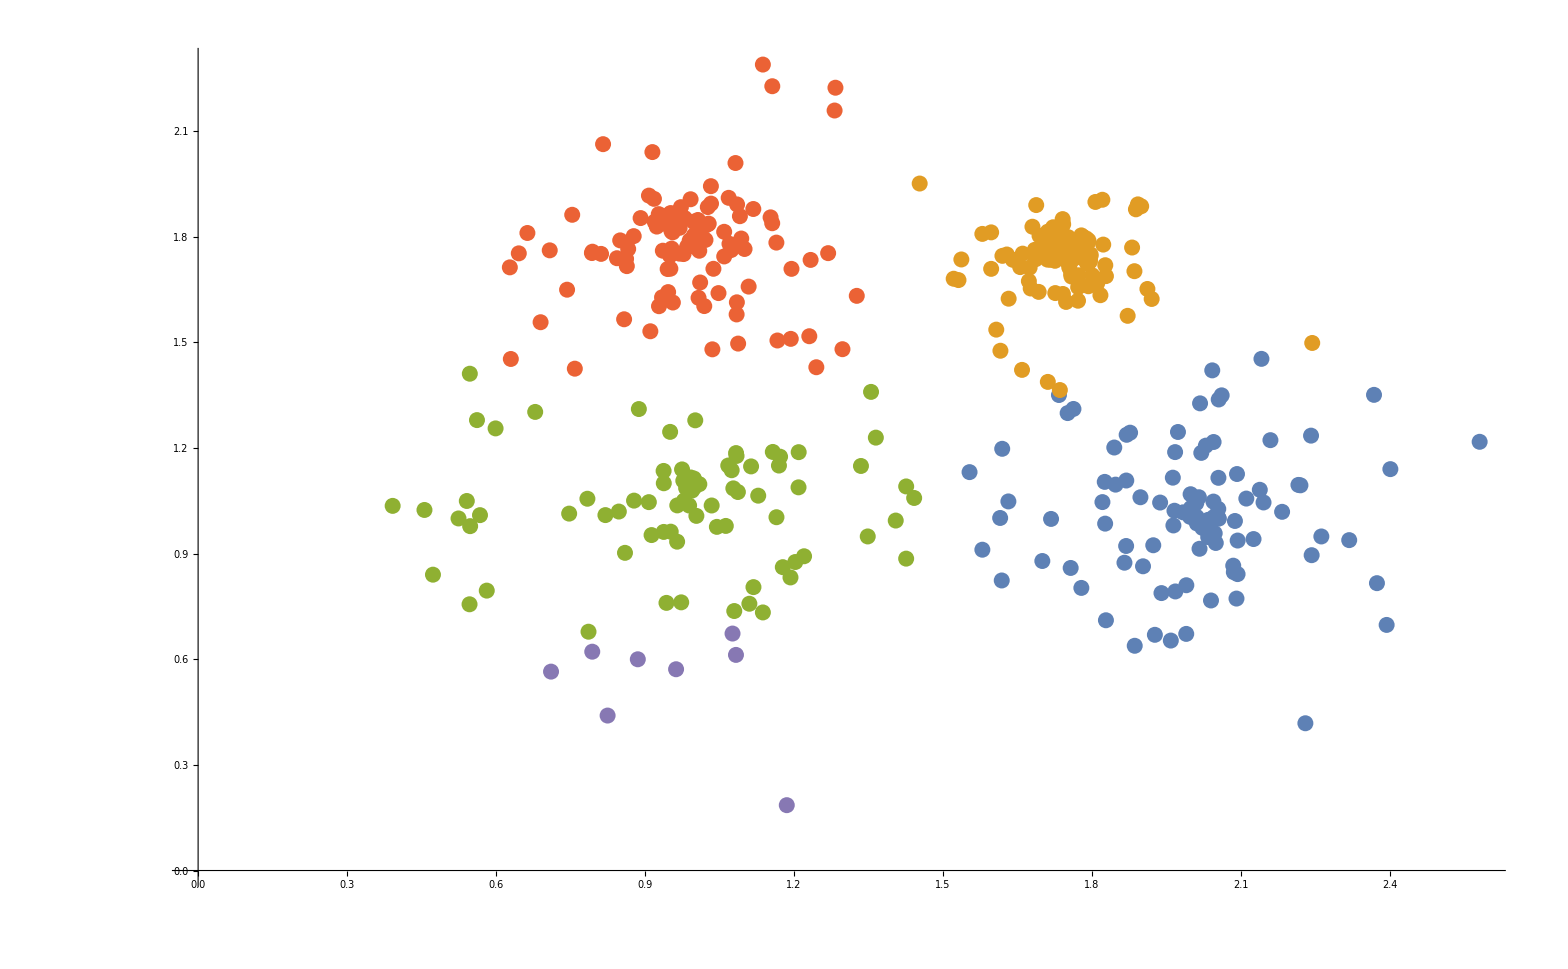
```mathematica
-Graphics--Graphics-
```

#### Step1

Set integer q'≥1,  and replace x(t) in X=={x((s-1)δt),x((s-2)δt),…,x(0)} with Δt==(q'-1)δt  then we get:

     x^Δt(t)==∑_(i=1)^q' x(t-(i-1)δt)/q'

#### Step2

Let parameters Θ=={θ_1,⋯,θ_K} (characterizes our coarse-grained partition.) and loss function:

    L(Θ)=∑_(k=1)^K ∑_(i==q'-1)^(s-1) γ_k(i δ t)||x^(Δ t)(i δ t) - θ_k^Δt((||)_2)^2

where 

    γ_k(t)=={1    k==argmin_j||x^(Δ t)(i δ t) - θ_k^Δt((||)_2)^2
0    otherwise

is the weight of the k-th cluster at time t==iδt.

#### Step3

Collect initial data X_0=={x(-(q-1)δt),x(-(q-2)δt),…,x(0)} over an interval [-Δτ,0] with Δτ==(q-1)δt and calculate its average x^Δτ==∑_(i=1)^q x(t-(i-1)δτ)/q , the initial data in the prediction stage are independent of t he training dataset and the affiliation function S is given by: S==argmin_k||x^(Δ τ) - θ_k^Δt(||)_2 depends on both Δt and Δτ

#### Step4

Now estimate the PDF p^k(A_t) .

    Get a sequence of observations  x(t') (independent of the training data set X) and get the corresponding time series A_t' of the target variable.

    Using S==argmin_k||x^(Δ τ) - θ_k^Δt(||)_2 compute the membership sequence S_t'==S(X_t') for every time t'. 

    For given lead time t, for each k∈{1,…,K} collect:
    
    A_t^k=={A_(t+t'):S_t'==k}

    For the distribution boundaries A_0<A_1<⋯ and compute the occurrence frequencies (p̂)_t^k(A_i)==N_i/N
, N_i is the number of elements of A_t lying in [A_(i-1),A_i], and N==∑_i N_i. And our estimators  (p̂)_t^k(A_i) 
converge to our continuous PDFs p^k(A_t) from p^k(A_t)==p(A_t|S==k) .

We can get the p^k(A_t),p_eq(A_t), and π_k using the similar method

## Qualifying the model error in long-range forecasts

#### Step1

We have an imperfect model with prediction probabilities p^Mk(A_t)==p^M(A_t|S==k) and Markov property
 
     p^M(A_t,X_0,S)==p^M(A_t|X_0,S)p(X_0|S)p(S)==p^M(A_t|X_0)p(X_0|S)p(S)
 
    suppose the perfect and imperfect model have the same initial data and cluster affiliation function:

    p^M(X_0|S)==p(X_0|S) and p^M(S)==p(S)) 

    and the coarse-grained forecast distributions can be determined via:

    p^M(A_t|S)==∫d X_0 p^M(A_t|X_0)p(X_0|S)

    Similarly, 

    D_t^MK==∑_(k=1)^K π_k D_t^Mk,   with D_t^Mk==P(p^Mk(A_t),p_eq^M(A_t))

    δ_t^M==1-exp(-2 D_t^M)

    ϵ_eq==1-exp(-2 E_eq) and ϵ_eq≪1    E_eq==P(p_eq(A_t),p_eq^M(A_t))

#### Step2

The expected error in the coarse-grained forecast distributions is expressed in 

    E_t^K==∑_(k=1)^K π_k E_t^k,   with E_t^k==P(p^k(A_t),p^Mk(A_t)), π_k==p(S==k)

    where 

    ϵ_t==1-exp(-2 E_t^K),  ϵ_t∈[0,1)

    E_t==E_t^K+l_t^K-g_t^K

    where 

    l_t^K==∑_(S=1)^K ∫d X_0∫d A_t p(A_t,X_0,S)log(p(X_0|A_t,S))/(p(X_0|S))

    g_t^K==∑_(S=1)^K ∫d X_0∫d A_t p(A_t,X_0,S)log(p^M(A_t|X_0))/(p^M(A_t|S))

    and g_t^K≤l_t^K, E_t≥E_t^K;

    We define the expected score S_t^K==H-D_t^K+E_t^K

## Application with three-mode dyad model and its imperfect simulation

Perfect model:

    dx==(Ix y_1+L_1 y_1+L_2 y_2+F+Dx)dt

    d y_1==(-I x^2-L_1 x-γ_1 ϵ^-1 y_1)dt+σ_1 ϵ^(-1/2)d W_1

    d y_2==(-L_2x-γ_2 ϵ^-1 y_2)dt+σ_2 ϵ^(-1/2)d W_2

    where ϵ controls the timescale.

By MTV mode-reduction procedure we got a imperfect but one dimension   

    dx==(F̃+ax+b x^2-c x^3)dt+(α-βx)d W_1+σd W_2

    where

    F̃==F+ϵ(σ_1^2 I L_1)/(2 γ_1^2)

    a==D+ϵ((σ_1^2 I^2)/(2 γ_1^2)-(L_1^2/γ_1+L_2^2/γ_2))

    b==-ϵ(2I L_1)/γ_1

    c==ϵ I^2/γ_1

    α==ϵ^(1/2)(σ_1 L_1)/γ_1,  β==-ϵ^(1/2)(σ_1 I)/γ_1,  σ==ϵ^(1/2)(σ_2 L_2)/γ_2

for its PDF are simple:

    p_eq^M(x)==N/(((βx-α)^2+σ^2)^(ã))exp(d̃ atan((βx-α)/σ))exp((b̃ x-c̃ x^2)/B^4)

    where:

    ã==1-(-3 α^2 c+a β^2+2αbβ+c σ^2)/β^4

    b̃==2b β^2-4cαβ,  c̃==c β^2

    d̃==d'/σ+d'' σ,  d'==(2 α^2 bβ-2 α^3 c+2αa β^2+2 β^3 F̃)/β^4

    d''==(6cα-2bβ)/β^4

## Numerical Simulation

Let I==1,σ_1==1.2,σ_2==0.8 , D==-2,L_1==0.2,L_2==0.1, F==0,γ_1==0.1,γ_2==0.6and ϵ = 0.1 or 1.

Make a numerical simulation with 10^-4 time steps and 2000 natural time units

### Perfect Model - The three-mode dyad model ε = 0.1

```mathematica
proc = ItoProcess[{ⅆx[t]==(x[t]*y[t]+0.2*y[t]+0.1*z[t]-2*x[t]) ⅆt,ⅆy[t]==(-x[t]^2-0.2*x[t]-0.1*0.1^-1*y[t]) ⅆt+1.2*0.1^(-1/2)*ⅆw1[t],
ⅆz[t]==(-0.1*x[t]-0.6*0.1^-1*z[t]) ⅆt+0.8*0.1^(-1/2)*ⅆw2[t]},{x[t],y[t],z[t]},{{x,y,z},{0,0,0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];
path3=RandomFunction[proc,{0.,1000,0.01},Method->"StochasticRungeKutta"];
ListLinePlot[path3]
Mean[path3]
Variance[path3]
Skewness[path3]
Kurtosis[path3]
```

-Graphics-

{0.231859,-0.41024,0.00949723}

{0.398661,6.01863,0.553404}

{3.61067,-0.0796195,-0.0125142}

{20.2296,2.98477,3.00585}

## Perfect Model - The three-mode dyad model ε = 1

```mathematica
proc = ItoProcess[{ⅆx[t]==(x[t]*y[t]+0.2*y[t]+0.1*z[t]-2*x[t]) ⅆt,ⅆy[t]==(-x[t]^2-0.2*x[t]-0.1*1^-1*y[t]) ⅆt+1.2*1^(-1/2)*ⅆw1[t],
ⅆz[t]==(-0.1*x[t]-0.6*1^-1*z[t]) ⅆt+0.8*1^(-1/2)*ⅆw2[t]},{x[t],y[t],z[t]},{{x,y,z},{0,0,0}},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];
path4=RandomFunction[proc,{0.,1000,0.01},Method->"StochasticRungeKutta"];
ListLinePlot[path4]
Mean[path4]
Variance[path4]
Skewness[path4]
Kurtosis[path4]
```

-Graphics-

{0.0582167,-1.2869,0.0426933}

{0.0948598,5.18357,0.468929}

{2.84724,-0.378902,0.047132}

{12.9655,2.49785,3.02598}

## Imperfect Model - Scalar Stochastic Model ε = 0.1

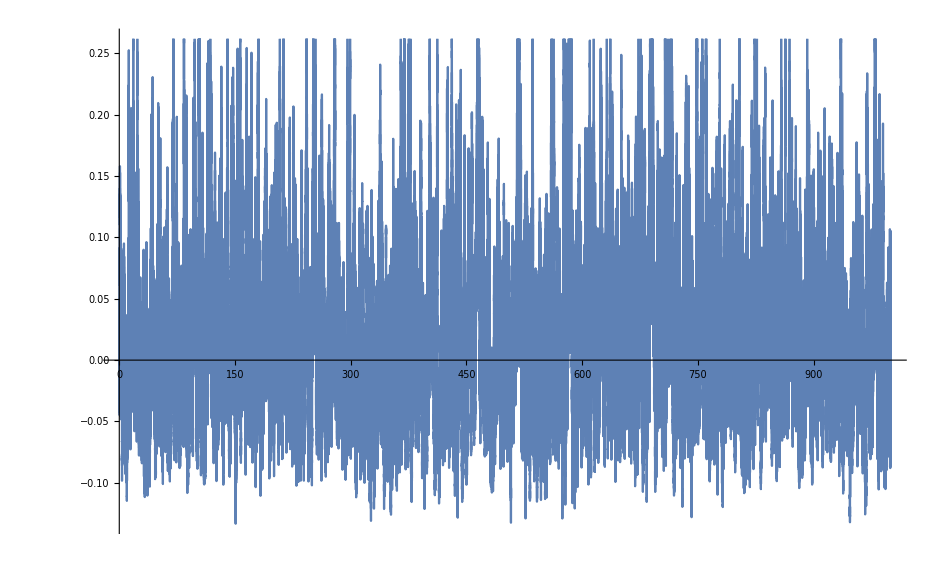

0.0203883

0.0055358

1.37614

6.48161

```mathematica
proc = ItoProcess[ⅆx[t]==(tutaF+a*x[t]+b*x[t]^2-c*x[t]^3) ⅆt+(alpha-beta*x[t])ⅆw1[t]+sigmaⅆw2[t],x[t],{x,0},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];proc1=proc/.{tutaF->0.04,a->-1.809,b->-0.067,c->0.167,alpha->0.105,beta->-0.634,sigma->0.063};
Subscript[path, 0.1]=RandomFunction[proc1,{0.,1000,0.01},Method->"StochasticRungeKutta"];
ListLinePlot[Subscript[path, 0.1]]
Mean[Subscript[path, 0.1]]
Variance[Subscript[path, 0.1]]
Skewness[Subscript[path, 0.1]]
Kurtosis[Subscript[path, 0.1]]
```

## Imperfect Model - Scalar Stochastic Model ε = 1

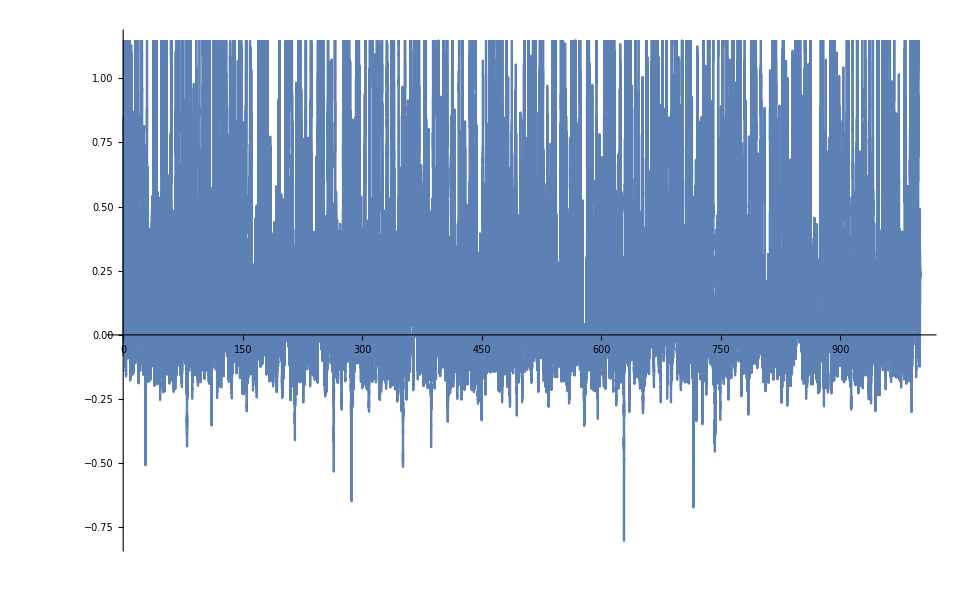

0.172214

0.125916

2.27916

11.004

```mathematica
proc = ItoProcess[ⅆx[t]==(tutaF+a*x[t]+b*x[t]^2-c*x[t]^3) ⅆt+(alpha-beta*x[t])ⅆw1[t]+sigmaⅆw2[t],x[t],{x,0},t,{w1\[Distributed]WienerProcess[],w2\[Distributed]WienerProcess[]}];proc2=proc/.{tutaF->0.4,a->-0.092,b->-0.667,c->1.667,alpha->0.333,beta->-2,sigma->0.2};
Subscript[path, 1]=RandomFunction[proc2,{0,1000,0.01},Method->"StochasticRungeKutta"];
ListLinePlot[Subscript[path, 1]]
Mean[Subscript[path, 1]]
Variance[Subscript[path, 1]]
Skewness[Subscript[path, 1]]
Kurtosis[Subscript[path, 1]]
```

Histogram::hbins: The bin specification Probability cannot be used to determine either how many or which bins to use.

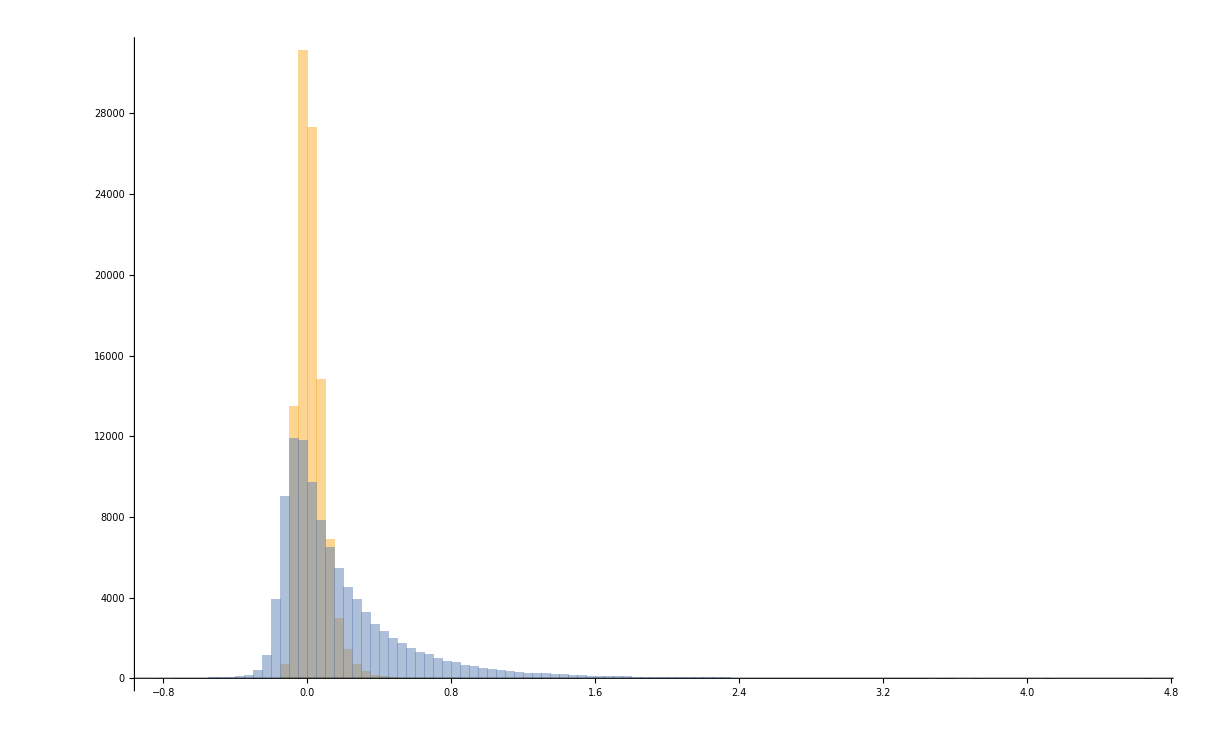

```mathematica
Histogram[{Subscript[path, 0.1],Subscript[path, 1]}, "Probability"]
```

## Back to the results in paper

-Graphics-
-Graphics-

## Long-range predictability in a perfect model environment

### Predictability on time

A_t=x(t) be the target variable for prediction which come from three-mode system and its one dimension system with ϵ==0.1 or 1
  
    Training time series of length T = 400

    Sample step length δt==0.01

    Sample number s==40000

    Running average interval Δt==1.6==160δt

    When  ϵ==0.1, Δt≃2.2 τ_c, T≃550 τ_c

    When  ϵ==1, Δt≃τ_c, T≃250 τ_c

Use algorithm to calculate the predictability score δ_t, δ_t^M, ϵ_t.

Three score with partition K∈{2,…,5}

-Graphics-

### Predictability on space

-Graphics-

Solid line is Time-dependent prediction probabilities for mode PDFs p^k(x(t)) in perfect model with cluster k=1,4.

    Dashed line is that  p^Mk(x(t)) in the imperfect model. 

    The error in the imperfect model is significantly higher for ϵ = 1 than 0.1.

    The error in the imperfect models is more significant for large and positive values of x